```mathematica
fXY[n_,k_][x_?NumericQ,y_?NumericQ]:=BesselJ[n,k Sqrt[x^2+y^2]] Cos[n ArcTan[y,x]]
wavePattern[n_,j_]:=Module[{k0=N[BesselJZero[n,j]]},DensityPlot[fXY[n,k0][x,y],{x,-1.1,1.1},{y,-1.2,1.1},RegionFunction->Function[{x,y},x^2+y^2<1],ColorFunction->"BlueGreenYellow",PlotPoints->100,MaxRecursion->0,Epilog->Inset[Grid[{{"n",n},{"j",j}},Frame->All],{-.9,.9}],BaseStyle->{FontFamily->"Arial"}]]
Show[GraphicsGrid@Table[wavePattern[m,n],{m,0,2},{n,1,3}],ImageSize->700]
```

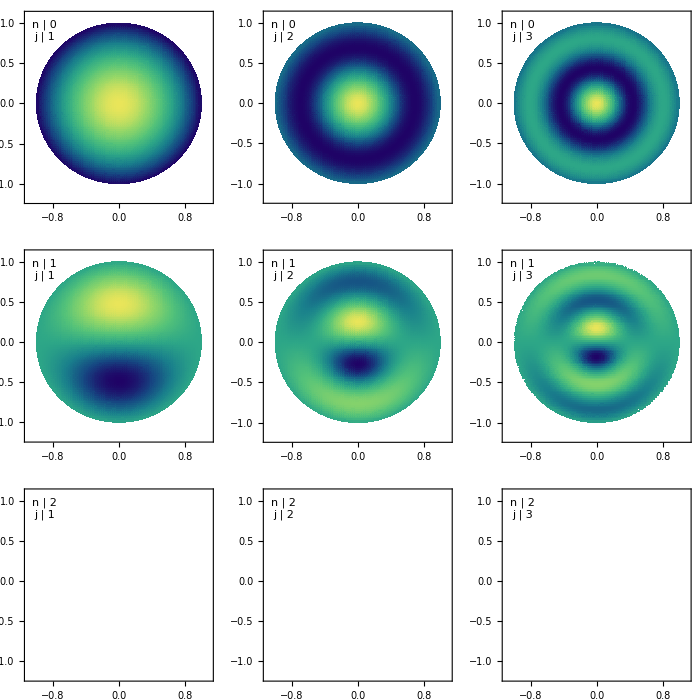

```mathematica
(*wavePattern[n_,j_]:=Module[{k0=N[BesselJZero[n,j]]},DensityPlot[fXY[n,k0][x,y],{x,-1.1,1.1},{y,-1.2,1.1},RegionFunction->Function[{x,y},x^2+y^2<1],ColorFunction->Function[{x},Blend[{White,Darker@Brown,White},2 ArcTan[10 x]/Pi+.5]],ColorFunctionScaling->False,PlotPoints->100,MaxRecursion->0,Epilog->Inset[Grid[{{"n",n},{"j",j}},Frame->All],{-.9,.9}],BaseStyle->{FontFamily->"Arial"}]]

Show[GraphicsGrid@Table[wavePattern[m,n],{m,0,2},{n,1,3}],ImageSize->700]*)
```